# AM1b - laboratorium nr 2, 4.03.2022

#### Zadanie 2. Narysuj, używając funkcji ParametricPlot oraz ParametricPlot3D:

Okrąg { (x,y) : x^2 + y^2 = 1 } podniesiony na powierzchnię walca { (x, y, z) : x^2+ y^2 = 1 } w taki sposób, że punkty (1,0) oraz (-1,0) dostają z-ową współrzędną równą 0, a punkty (0,1) i (-1,0) - równą 1.

```mathematica
(*ParametricPlot3D[{Sin[x], Cos[x], z}, {x, 0, 2π}, {z, -1, 1}, LabelStyle->"Section", AxesLabel->{x,y,z}]*)
circ[t_] := {Cos[t], Sin[t], 0};
newCirc[t_] = {0, 0, 0} + RotationTransform[{{1, 0, 0}, {0, 1, 1}}][circ[t]];
ParametricPlot3D[newCirc[t], {t, 0, 2 π},  LabelStyle->"Section", AxesLabel->{x,y,z}]
```

-Graphics3D-

Spiralę na płaszczyźnie mającą tę własność, że jej punkty przecięcia z dowolną półprostą wychodzącą z punktu (0, 0) tworzą na niej ciąg arytmetyczny.

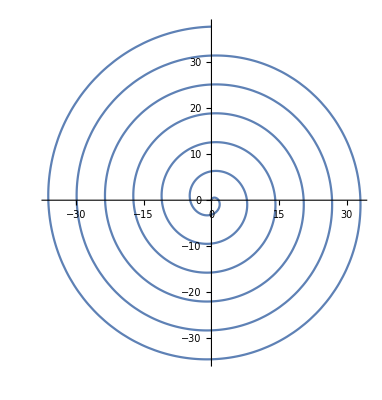

```mathematica
ParametricPlot[{u Sin[u], u Cos[u]}, {u, 0 , 12π}]
```

Powyższą spiralę  podniesioną na powierzchnię stożka { z = √(x^2 + y^2) }.

```mathematica
ParametricPlot3D[{u Sin[u], u Cos[u], u}, {u, 0 , 12π},LabelStyle->"Section", AxesLabel->{x,y,z}]
```

-Graphics3D-

Stożek i spiralę na jednym rysunku.

```mathematica
Show[ParametricPlot3D[{u Sin[u], u Cos[u], 0}, {u, 0, 12π}],ParametricPlot3D[{u Sin[u], u Cos[u], u}, {u, 0 , 12π}], PlotRange->All]
```

-Graphics3D-

#### Zadanie 3. Narysuj, używając funkcji ParametricPlot3D:

Torus dwuwymiarowy umieszczony w przestrzeni trójwymiarowej w taki sposób, aby wyznaczające go okręgi miały promienie 1 i 3.

```mathematica
pp3 = ParametricPlot3D[{(2 + Cos[v]) Cos[u], (2 + Cos[v]) Sin[u], 
   Sin[v]}, {u, 0, 2 Pi}, {v, 0, 2 Pi}]
```

-Graphics3D-

Przykład :

```mathematica
ParametricPlot3D[{1+t+s,t+s,t},{t,-2,2},{s,-2,2},AxesLabel->{x,y,z}]
```

-Graphics3D-

Fragment sfery dwuwymiarowej o promieniu 1, odcięty na wysokości równoleżników 45°N i 60°S.

#### Zadanie 4. Narysuj, używając funkcji Plot oraz Manipulate:

Wykres funkcji f(x) = 1/(σ √(2π))exp(-(x-μ)^2/(2 σ^2)). Jak zmienia się on wraz z μ i σ?

```mathematica
Manipulate[Plot[
  {PDF[NormalDistribution[σ, μ], x]},
  {x, -5, 5}, Filling -> Axis, Evaluated->True], {σ, 0.5, 1}, {μ, 1, 2}]
```

Eksperymentując z powyższym wykresem podaj przykład funkcji g(x), która:
- w x = 1 przyjmuje wartość 1,
- w x = -2 przyjmuje wartość -1,
- poza przedziałami [-2.5,-1.5] oraz [0.8,1.2] jest bliska 0 (np. |g(x)| < 0.1)

```mathematica
g[x_]:=
```

Sprawdzenie

```mathematica
err = 1/10;
Resolve[
   ForAll[x,
      Between[x,{{-25/10,-15/10},{8/10,12/10}}] ||
      Abs[g[x]]<err 
   ],
Reals]
```

∀_{x}((-5/2≤x&&x≤-3/2)||(4/5≤x&&x≤6/5)||Abs[g[x]]<1/10)